```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPAp_mub0/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub0/buffer/Zphi.dat"]];
T0=Flatten[Import["./LPAp_mub0/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPAp_mub300/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub300/buffer/Zphi.dat"]];
T0=Flatten[Import["./LPAp_mub300/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub300=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPAp_mub400/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub400/buffer/Zphi.dat"]];
T0=Flatten[Import["./LPAp_mub400/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub400=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPAp_mub500/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub500/buffer/Zphi.dat"]];
T0=Flatten[Import["./LPAp_mub500/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPAp_mub600/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub600/buffer/Zphi.dat"]];
T0=Flatten[Import["./LPAp_mub600/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub600=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub600=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
```

## Plot

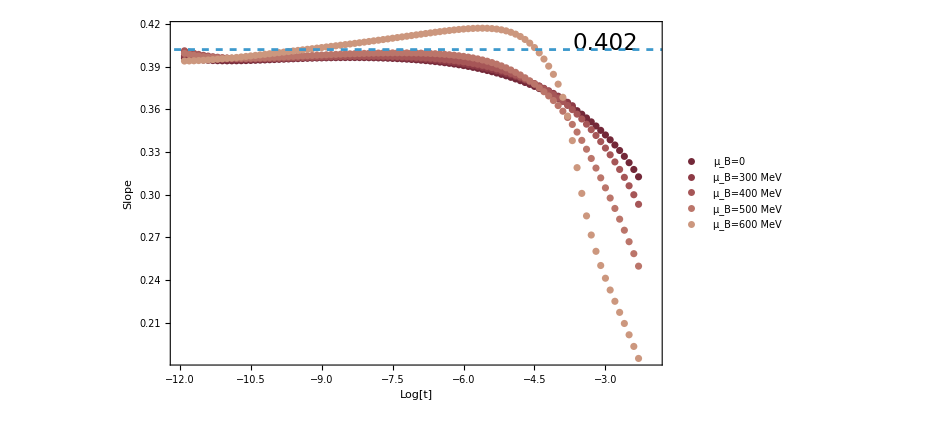

```mathematica
plotT=Show[ListPlot[{b1mub0,b1mub300,b1mub400,b1mub500,b1mub600(*,b1mub650*)},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["Slope",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.0714}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=300 MeV","μ_B=400 MeV","μ_B=500 MeV","μ_B=600 MeV","μ_B=650 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},(*{0.3,0.43}*)All},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.402},{10,0.402}},PlotStyle->Dashed],ImageSize->700,Background->None,Epilog->{Text[Style["0.402",23],{-3,0.406}]}]
```